Assuming that ExportSVG is installed, for example as usual in FileNameJoin[{$UserBaseDirectory, “Applications”}]

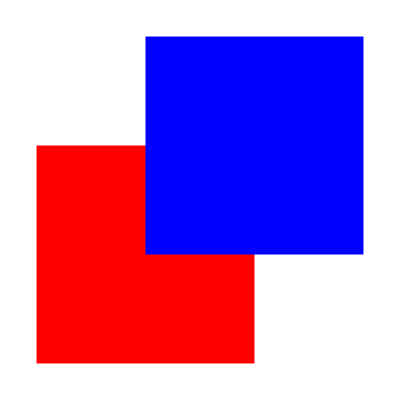

```mathematica
<<ExportSVG`
gr=Graphics[{Red,Rectangle[{0,0},RoundingRadius->0.1],Blue,Rectangle[{0.5,0.5}]}]
ExportSVG[gr]
```

(The result is flipped around the horizontal axis:)

<?xml version='1.0' encoding='UTF-8'?>
<svg xmlns='http://www.w3.org/2000/svg'
    xmlns:xlink='http://www.w3.org/1999/xlink'
    width='278.4pt'
    height='278.4pt'
    viewBox='0.0 0.0 1.5 1.5'
    preserveAspectRatio='xMinYMin meet'>
 <rect x='0'
     y='0'
     width='1'
     height='1'
     rx='0.1'
     ry='0.1'
     fill='rgb(100%,0%,0%)' />
 <rect x='0.5'
     y='0.5'
     width='1'
     height='1'
     rx='0'
     ry='0'
     fill='rgb(0%,0%,100%)' />
</svg>

```mathematica
SystemOpen@Export["~/Desktop/test.svg",ExportSVG[gr],"Text"];
```